```mathematica
(* Filename: Errors_vs_Time_By_w2_SS_tuck_A1_2A1_sym_DN
*)
(* Ver. 0 (28-Aug-2025) *)
(*
This file is a program code in Mathematica to get a plot about errors in Fig. 2.
*)
(*
Note that the following files should be excuted before this program:
a) Errors_By_wo2_SS_tuck_A1_2A1_sym_DN,
    b) Time_By_w2_SS_tuck_A1_2A1_sym_DN.
*)
```

```mathematica
fdim=2;
```

```mathematica
difflistMomAndTimeBForAve=Table[{},{ii,1,fdim}];
tmpMini=Table[{},{ii,1,5}];
For[ii=1, ii≤fdim, ii++,
tmpMini[[1]]={Log[2,timeB4Ave],Log[2,errorMomB4Ave[[ii]]]};
tmpMini[[2]]={Log[2,timeB8Ave],Log[2,errorMomB8Ave[[ii]]]};
tmpMini[[3]]={Log[2,timeB16Ave],Log[2,errorMomB16Ave[[ii]]]};
tmpMini[[4]]={Log[2,timeB32Ave],Log[2,errorMomB32Ave[[ii]]]};
tmpMini[[5]]={Log[2,timeB64Ave],Log[2,errorMomB64Ave[[ii]]]};
difflistMomAndTimeBForAve[[ii]]=Table[tmpMini[[ii]],{ii,1,5}];
];
```

```mathematica
plotlistMomAndTimeBForAve=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
plotlistMomAndTimeBForAve[[ii]]=ListPlot[difflistMomAndTimeBForAve[[ii]],PlotMarkers->{Graphics[{EdgeForm[{Thickness[0.1],Blue}],Opacity[0],Polygon[{{0,0},{1,0},{0.5,1}}]}],Scaled[0.035]}];
];
```

numSubSetForData=8

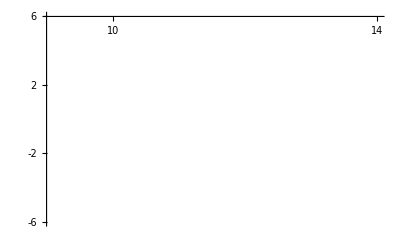

```mathematica
ll=0.03;
Print["numSubSetForData=",numSubSetForData];
ii=1;
Show[plotlistMomAndTimeBForAve[[ii]],PlotRange->{{9+0.06,14},{-6,6}},AxesOrigin->{9,6},Ticks->{Table[{1ii,ToString[1ii],ll},{ii,2,20}],Table[{-2ii,ToString[-2ii],ll},{ii,-3,8}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```